```mathematica
τ[vj_]:=φ1j/(1+Exp[-φ2j*(vj+φ3j)])-φ1j/(1+Exp[-φ2j*φ3j]);
D[τ[v],v]
k=D[τ[v],v]/.v->0
```

(ⅇ^(-φ2j (v+φ3j)) φ1j φ2j)/((1+ⅇ^(-φ2j (v+φ3j)))^2)

(ⅇ^(-φ2j φ3j) φ1j φ2j)/((1+ⅇ^(-φ2j φ3j))^2)

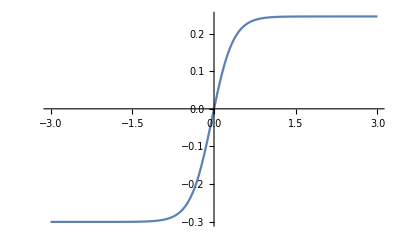

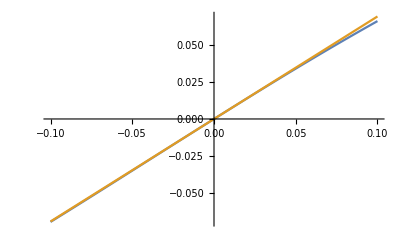

```mathematica
Joint1={φ1j->0.54615,φ2j->5.1181,φ3j->0.039533};
Plot[τ[v]/.Joint1,{v,-3,3}]
Plot[{τ[v]/.Joint1,(k/.Joint1)*v},{v,-0.1,0.1}]
```